Towards critical and supercritical electromagnetic fields

M. Marklund, T. G. Blackburn, A. Gonoskov, J. Magnusson, S. S. Bulanov, A. Ilderton, arXiv:2209.11720v1 (2022)
Notebook: Óscar Amaro, January 2023 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

## Figure 2

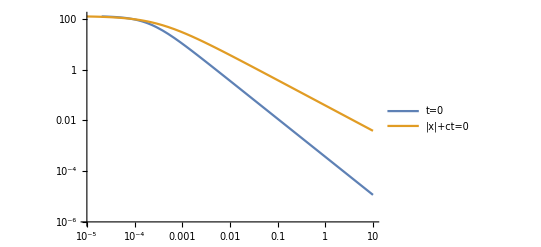

```mathematica
Clear[χ,a0,f,λ,P,αχ23,χa03,fχ3,γ0,ϵ0]
Clear[A,R,Dnm]
LogLogPlot[{A(Abs[(r+ct)/R]^1.5+1)^(-1) (Abs[ct/Dnm]+1)^(-1)/.{A->130,R->0.2,Dnm->0.3,ct->0,r->coor 10^3},A (Abs[r/Dnm]+1)^(-1)/.{A->130,R->0.2,Dnm->0.3,r->coor 10^3}},{coor,10^-5,10^1},PlotRange->{10^-6,10^2.1},PlotLegends->{"t=0","|x|+ct=0"}]
```

## Appendix A

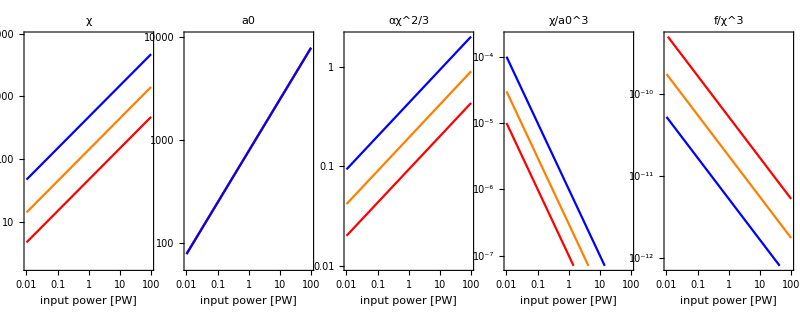

```mathematica
Clear[χ,a0,f,λ,P,αχ23,χa03,fχ3,γ0,ϵ0]

χ=3.7 ϵ0 P^0.5 / λ; (*[]*)
a0 = 780 P^0.5;
f=3.6 10^-6 P/λ^2;
αχ23 = 0.017 ϵ0^(2/3) P^(1/3)/λ^(2/3);
χa03=7.8 10^-9 ϵ0/P/λ;
fχ3=7 10^-8 λ/ϵ0^3 / P^0.5;

γ0=2 10^4;
ϵ0=γ0 0.511 10^-3;(* [GeV] *)

imgsz=250;
GraphicsRow[{
LogLogPlot[{χ/.{λ->0.8},χ/.{λ->0.8/3},χ/.{λ->0.8/10}},{P,0.01,100},AspectRatio->2,ImageSize->imgsz,Frame->True,PlotLabel->"χ",FrameLabel->{"input power [PW]",""},PlotRange->{2,9000},PlotStyle->{Red,Orange,Blue}],
LogLogPlot[{a0/.{λ->0.8},a0/.{λ->0.8/3},a0/.{λ->0.8/10}},{P,0.01,100},AspectRatio->2,ImageSize->imgsz,Frame->True,PlotLabel->"a0",FrameLabel->{"input power [PW]",""},PlotRange->{60,10^4},PlotStyle->{Red,Orange,Blue}],
LogLogPlot[{αχ23/.{λ->0.8},αχ23/.{λ->0.8/3},αχ23/.{λ->0.8/10}},{P,0.01,100},AspectRatio->2,ImageSize->imgsz,Frame->True,PlotLabel->"αχ^2/3",FrameLabel->{"input power [PW]",""},PlotRange->{0.01,2},PlotStyle->{Red,Orange,Blue}],
LogLogPlot[{χa03/.{λ->0.8},χa03/.{λ->0.8/3},χa03/.{λ->0.8/10}},{P,0.01,100},AspectRatio->2,ImageSize->imgsz,Frame->True,PlotLabel->"χ/a0^3",FrameLabel->{"input power [PW]",""},PlotRange->{7 10^-8,2 10^-4},PlotStyle->{Red,Orange,Blue}],
LogLogPlot[{fχ3/.{λ->0.8},fχ3/.{λ->0.8/3},fχ3/.{λ->0.8/10}},{P,0.01,100},AspectRatio->2,ImageSize->imgsz,Frame->True,PlotLabel->"f/χ^3",FrameLabel->{"input power [PW]",""},PlotRange->{8 10^-13,5 10^-10},PlotStyle->{Red,Orange,Blue}]
},Spacings->0,ImageSize->800]
```